# Simulations

## Parameters

```mathematica
ClearAll[cg,Vg,R, δlac, mE,y,ξunit];
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0022/2;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=1;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[9/10,"Nanograms"]Quantity["Days"/"Milliliters"]);
```

## Functions

Basics

```mathematica
ClearAll[Mg,δ,λ,λmax,vl]
δ[sg_,sl_]:=δlac sl;
λ[sg_,sl_][vg_,vatp_]:=y(vatp-mE)-δ[sg,sl];
λmax[sg_,sl_,ξ_]:=λ[sg,sl][0.,vatpmax[ξ]]
Mg[ξ_]:=Piecewise[{{Vg, ξ≤cg/Vg}, {cg/ξ, ξ>cg/Vg}}];
vl[vg_,vatp_]:=1/19(vatp-40vg);
vo[vg_,vatp_]:=1/19(vatp-2vg);
vgmin[ξ_][vatp_]:=1/2 Max[1/20 vatp,vatp-19R];
vgmax[ξ_][vatp_]:=Min[Mg[ξ],1/2 vatp];
vatpmax[ξ_]:=2Mg[ξ]+19Min[2Mg[ξ],R];
```

```mathematica
(* Test *)
Module [{ξ,β, testVatp, testVg},
ξ = 2;
β = 2;
(* Print[Style["Total tests", 35]];
Print[Style["Parameters: ", 20, Red]];
Print["Glucose in feed (cg): ", cg//N];
Print["Universal max glc uptake (Vg): ", Vg//N];
Print["Universal max respiration (R): ", R//N];
Print["Date rate doto lactate (δlac): ", δlac//N];
Print["Maintenance ATP demand (mE): ", mE//N];
Print["Units of atp needed to produce a unit of biomass (y): ", y//N];
Print["Stoichiometric coeficient of fermentation (2): ", 2];
Print["Stoichiometric coeficient of respiration (19): ", 19];
Print["Units of ξ (ξunit)", ξunit//N];
Print["Number of maintained cells per unit of fresh culture per unit of time (ξ): ", ξ//N];
Print["\"Heterogenity coeficient\" (β): ", β//N];
Print[""]; *)

Print[Style["Polytope: ", 20, Red]];
Print["Global min vatp value (0): ", 0];
Print["Global max vatp value (vatpmax[ξ_]): ", vatpmax[ξ]//N];
Print["Local min vatp value: Not implemented"];
Print["Local max vatp value: Not implemented"];

Print["Global min vg value (vgmin[ξ_][0]): ", vgmin[ξ][0]//N];
Print["Global max vg value (vgmin[ξ_][vatpmax]): ", vgmax[ξ][vatpmax[ξ]]//N];
Print["Local min vg value (vgmin[ξ_][vatp_]) at vatpmax/2: ", vgmin[ξ][vatpmax[ξ]/2]//N];
Print["Local max vg value (vgmax[ξ_][vatp_]) at vatpmax/2: ", vgmax[ξ][vatpmax[ξ]/2]//N];
Print["Polytope vertexes (vertexes[ξ_]): ", vertices[ξ]//N];
Print[""];

]
```

Polytope:

Global min vatp value (0): 0

Global max vatp value (vatpmax[ξ_]): 8.6

Local min vatp value: Not implemented

Local max vatp value: Not implemented

Global min vg value (vgmin[ξ_][0]): 0.

Global max vg value (vgmin[ξ_][vatpmax]): 0.5

Local min vg value (vgmin[ξ_][vatp_]) at vatpmax/2: 0.1075

Local max vg value (vgmax[ξ_][vatp_]) at vatpmax/2: 0.5

Polytope vertexes (vertexes[ξ_]): {{0.,0.},{1.,0.5},{8.6,0.5},{8.,0.2}}

```mathematica
polytope[ξ_][vg_,vatp_]:=Boole[0≤vg≤Mg[ξ]∧vl[vg,vatp]≤0∧0≤vo[vg,vatp]≤R];

polytopeother[ξ_][vg_,vatp_]:=Boole[0≤vatp≤vatpmax[ξ]∧vgmin[ξ][vatp]≤vg≤vgmax[ξ][vatp]];
polytope1[ξ_][vg_,vatp_]:=Boole[0≤vatp<Min[19R,2Mg[ξ]]∧1/38 vatp≤vg≤1/2 vatp];
polytope2[ξ_][vg_,vatp_]:=Boole[2Mg[ξ]≤vatp≤Min[19R,vatpmax[ξ]]∧1/38 vatp≤vg≤Mg[ξ]];
polytope3[ξ_][vg_,vatp_]:=Boole[19R≤vatp≤2Mg[ξ]∧1/2(vatp-18R)≤vg≤1/2 vatp];
polytope4[ξ_][vg_,vatp_]:=Boole[Max[19R,2Mg[ξ]]≤vatp≤vatpmax[ξ]∧1/2(vatp-18R)≤vg≤Mg[ξ]];

polysum[ξ_][vg_,vatp_]:=polytope1[ξ][vg,vatp]+polytope2[ξ][vg,vatp]+polytope3[ξ][vg,vatp]+polytope4[ξ][vg,vatp];
vertices[ξ_]:=If[vatpmax[ξ]>19R,
{{0,0},{2Mg[ξ],Mg[ξ]},{vatpmax[ξ],Mg[ξ]},{20R,R/2}},
{{0,0},{2Mg[ξ],Mg[ξ]},{vatpmax[ξ],Mg[ξ]}}]
```

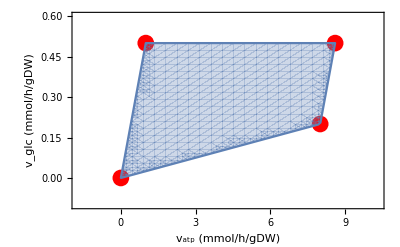

```mathematica
Module[{ξ=2},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpmax[ξ],1.2vatpmax[ξ]},{-0.2Mg[ξ],1.2Mg[ξ]}},
FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"},Frame->True,PlotRange->{{0,10},{0,0.6}},Axes->False],
RegionPlot[polytope[ξ][vg,vatp]==1,{vatp,0,vatpmax[ξ]},{vg,0,Mg[ξ]}]]]
```

Partition, expected values, variances, covariances

```mathematica
ClearAll[generateIntegral];

(* The integral in all the polytope *) 
generateIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]:=Module[{int0,int1,lb,ub},
int1=Simplify@Integrate[Exp[-β y(vatpmax[ξ]-vatp)]fun[vg,vatp],
{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
int0=Simplify@Integrate[fun[vg,vatp],{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
Piecewise[{{0, atplb≥atpub}, {int1, β>0}, {int0, β==0}}]];
```

```mathematica
generateIntegral[1][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{0,Min[20R,2Mg[ξ]]},{{ξ,vatp}↦vatp/40,{ξ,vatp}↦vatp/2}];
generateIntegral[2][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{2Mg[ξ],Min[20R,vatpmax[ξ]]},{{ξ,vatp}↦vatp/40,{ξ,vatp}↦Mg[ξ]}];
generateIntegral[3][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{20R,2Mg[ξ]},{{ξ,vatp}↦1/2(vatp-19R),{ξ,vatp}↦1/2 vatp}];
generateIntegral[4][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{Max[20R,2Mg[ξ]],vatpmax[ξ]},{{ξ,vatp}↦1/2(vatp-19R),{ξ,vatp}↦Mg[ξ]}];
```

```mathematica
ClearAll[fourDef]
fourDef[symbol_,fun_,norm_]:=Module[{},
ClearAll[symbol];
Do[symbol[i,β_,ξ_]:=Evaluate@generateIntegral[i][fun,β,ξ],{i,4}];
symbol[β_,ξ_]:=Sum[symbol[i,β,ξ],{i,4}]/norm[β,ξ]]
```

```mathematica
fourDef[z,{vg,vatp}↦1,{β,ξ}↦1];
fourDef[expVatp,{vg,vatp}↦vatp,z];
fourDef[expVg,{vg,vatp}↦vg,z];
```

```mathematica
ClearAll[ξ,β];
ξ = 2;
β = 2;
Print["Expected Z test: ", z[ξ,β]//N];
Print["Expected vatp test: ", expVatp[ξ,β]//N];
Print["Expected vg test: ", expVg[ξ,β]//N];ClearAll[ξ,β];
```

Expected Z test: 2.92978

Expected vatp test: 4.11622

Expected vg test: 0.296587

```mathematica
expVl[β_,ξ_]:=1/19(expVatp[β,ξ]-40expVg[β,ξ]);
```

```mathematica
ClearAll[pVatp,pVglc,pVglcVatp]
Do[pVatp[i,β_,ξ_,vatp0_]:=Evaluate@generateIntegral[i][{vg,vatp}↦DiracDelta[vatp-vatp0],β,ξ],{i,4}];
pVatp[β_,ξ_,vatp0_]:=Sum[pVatp[i,β,ξ,vatp0],{i,4}]/z[β,ξ];
pVglcVatp[β_,ξ_,vatp0_,vglc0_]:=pVatp[β,ξ,vatp0] Boole[vgmin[ξ][vatp0]≤vglc0≤vgmax[ξ][vatp0]]/(vgmax[ξ][vatp0]-vgmin[ξ][vatp0]);
pVglc[β_,ξ_,vg0_]:=Evaluate@Integrate[pVglcVatp[β,ξ,vatp,vg0],{vatp,2vg0,19Min[R,2vg0]+2vg0}];
```

```mathematica
pVglc[β_,ξ_]:=pVglc[β,ξ]={vg}↦Evaluate[Integrate[pVglcVatp[β,ξ,vatp,vg],{vatp,2vg,19Min[R,2vg]+2vg}]]
```

```mathematica
NIntegrate[pVglc[2.,10.][v],{v,0,1/2}]
```

1.

β = ∞ model (be sure to run this AFTER the previous cells)

```mathematica
expVg[∞,ξ_]:=Mg[ξ];
expVatp[∞,ξ_]:=vatpmax[ξ];
expVo[∞,ξ_]:=Min[2expVg[∞,ξ],R];
expVl[∞,ξ_]:=expVo[∞,ξ]-2expVg[∞,ξ];
```

Equilibrium

```mathematica
sgeq[β_,ξ_]:=cg-ξ expVg[β,ξ]
sleq[β_,ξ_]:=-ξ expVl[β,ξ]
Deq[β_,ξ_]:=λ[sgeq[β,ξ],sleq[β,ξ]][expVg[β,ξ],expVatp[β,ξ]]
Xeq[β_,ξ_]:=Deq[β,ξ]ξ
```

```mathematica
ClearAll[ξmax,ξDlocMax,ξDlocMin,ξDlocMinMax];On[Assert];
ξmax[β_]:=ξmax[β]=Module[{ξ},ξ/.First[Quiet[FindRoot[Deq[β,ξ]==0,{ξ,0.1,40 cg/mE}]]]];

ξDlocMinMax[β_]:=ξDlocMinMax[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β],ξ1,ξ2},
Assert[ξ0≤ξm];
If[ξ0==ξm,Return[{ξ0,ξm}]];
ξ1=Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ0,ξ0,ξm}];
ξ2=Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξm,ξ0,ξm}];
If[Not[ξ0<ξ1<ξm∨ξ0<ξ2<ξm],Return[{ξm,ξ0}]];
If[ξ1==ξ0||ξ1==ξm,ξ1=Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ2,ξ0,ξ2}]];
If[ξ2==ξ0||ξ2==ξm,ξ2=Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξ1,ξ1,ξm}]];
Return[{ξ1,ξ2}];
]
ξDlocMin[β_]:=ξDlocMin[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β]},Assert[ξ0≤ξm];If[ξ0<ξm,Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ0,ξ0,ξm}],ξ0]];
ξDlocMax[β_]:=ξDlocMax[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β]},Assert[ξ0≤ξm];If[ξ0<ξm,Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξm,ξ0,ξm}],ξm]];
ξDlocMin[β_]:=ξDlocMinMax[β]⟦1⟧;
ξDlocMax[β_]:=ξDlocMinMax[β]⟦2⟧;
```

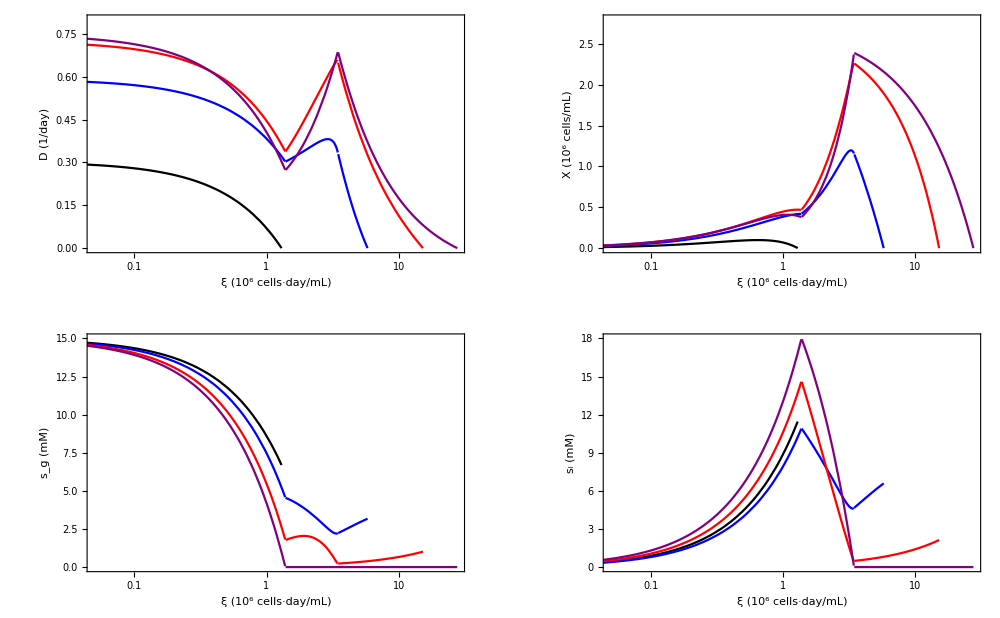

```mathematica
Module[{grid,βlist,colorList,plot,plotopts,ξunit,ξrange},
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[0.9,"Nanograms"]Quantity["Days"/"Milliliters"]);
βlist={0,1.99 100,1.99 1000,∞};colorList={GrayLevel[0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5]};
plotopts={PlotRange->Full,Frame->True,LabelStyle->Directive[GrayLevel[0],12],FrameStyle->GrayLevel[0],GridLines->None,Axes->None};
ξrange={-3,Log[ξmax[∞]ξunit]};
grid=GraphicsGrid[{
{Show[Table[LogLinearPlot[Deq[βlist⟦i⟧,ξ/ξunit]24,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,0.8}}],
Show[Table[LogLinearPlot[Xeq[βlist⟦i⟧,ξ/ξunit]1.111111,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","X (10^6 cells/mL)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,2.8}}]},
{Show[Table[LogLinearPlot[sgeq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_g (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,15}}],
Show[Table[LogLinearPlot[sleq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_l (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,18}}]}},
ImageSize->1000];
plot=Legended[grid,LineLegend[colorList,Table["λ_mβ = "<>ToString@NumberForm[N[β vatpmax[0]y],2],{β,βlist}]]];plot]
```

# Polytope

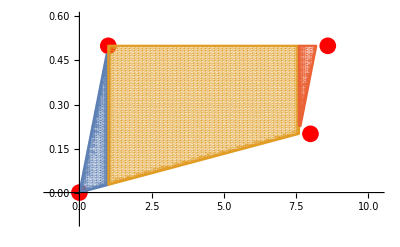

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-1,1.2vatpmax[ξ]},{-0.1,1.2Mg[ξ]}}],
RegionPlot[{polytope1[ξ][vg,vatp]==1,polytope2[ξ][vg,vatp]==1,polytope3[ξ][vg,vatp]==1,polytope4[ξ][vg,vatp]==1},{vatp,0,vatpmax[ξ]},{vg,0,Mg[ξ]},PlotPoints->60,MaxRecursion->5]]]
```